# Library of functions written to accompany the algorithms described in Modern Robotics: Mechanics, Planning, and Control.

# Author: Huan Weng, Mikhail Todes Functions also available in: Python, MATLAB Notes: Before using any of the functions in this library, each chapter’s cell needs to be evaluated. This can be done as a whole by highlighting everything (Ctrl + A) and then evaluating (Shift + Enter). Double click on the tabs at the side of each chapter to expand and view the code. At the start of each function is a description of what it does as well as an example showing how to use it. Quick tip: If you see a small T after braces, it means the transpose of that vector. This can be done the same way as accessing Greek letters in Mathematica. Press the Esc key, type “tr”, and then press the Esc key again.

# BASIC HELPER FUNCTIONS

```mathematica
(*NearZero[s_]:
  Takes a scalar.
Checks if the scalar is small enough to be neglected.
;
Example:
Input: judge = NearZero[-10^-7]
Output: True
*)

NearZero[s_]:=Abs[s]<10^-6
```

# CHAPTER 3: RIGID-BODY MOTION

```mathematica
(*RotInv[R_]:
  Takes a 3x3 rotation matrix.
Returns the inverse (transpose).
;
Example:
Input: invR = RotInv[{{0,0,1},{1,0,0},{0,1,0}}]
Output: {{0,1,0},{0,0,1},{1,0,0}}
*)

RotInv[R_]:=Rᵀ
```

```mathematica
(*VecToso3[omg_]:
   Takes a 3-vector (angular velocity).
Returns the skew symmetric matrix in so3.
;
Example:
Input: so3mat = VecToso3[{{1},{2},{3}}]
Output: {{0,-3,2},{3,0,-1},{-2,1,0}}
*)

VecToso3[omg_]:={{0,-omg[[3,1]],omg[[2,1]]},{omg[[3,1]],0,-omg[[1,1]]},{-omg[[2,1]],omg[[1,1]],0}}
```

```mathematica
(*so3ToVec[so3mat_]:
   Takes a 3x3 skew-symmetric matrix (an element of so(3)).
Returns the corresponding vector (angular velocity).
;
Example:
Input: omg = so3ToVec[{{0,-3,2},{3,0,-1},{-2,1,0}}]
Output: {{1},{2},{3}}
*)

so3ToVec[so3mat_]:={{so3mat[[3,2]],so3mat[[1,3]],so3mat[[2,1]]}}ᵀ
```

```mathematica
(*AxisAng3[expc3_]:
   Takes A 3-vector of exponential coordinates for rotation. 
Returns unit rotation axis omghat and the corresponding rotation angle theta.
The first element of the output is the unit rotation axis column vector (omghat) and the second element is theta.
;
Example:
Input: {omghat,theta} = AxisAng3[{{1,2,3}}ᵀ]//N
Output: {{{0.2672612419124244},{0.5345224838248488},{0.8017837257372732}},3.7416573867739413}
*)

AxisAng3[expc3_]:={expc3/Norm[expc3],Norm[expc3]}
```

```mathematica
(*MatrixExp3[so3mat]:
  Takes a so(3) representation of exponential coordinates.
Returns R in SO(3) that is achieved by rotating about omghat by theta from an initial orientation R=I.
;
Example:
Input: R = MatrixExp3[{{0,-3,2},{3,0,-1},{-2,1,0}}]//N//MatrixForm
Output: ({{-0.6949205576413118, 0.7135209905277876, 0.08929285886191213}, {-0.1920069727919994, -0.3037850443394705, 0.9331923538236468}, {0.6929781677417701, 0.6313496993837178, 0.34810747783026474}})
*)

MatrixExp3[so3mat_]:=Module[{omgtheta,omghat,theta,omgmat},omgtheta=so3ToVec[so3mat];If[NearZero[Norm[omgtheta]],Return[IdentityMatrix[3]],{omghat, theta} = AxisAng3[omgtheta];omgmat=so3mat/theta;Return[IdentityMatrix[3]+Sin[theta]*omgmat+(1-Cos[theta])*omgmat.omgmat]]]
```

```mathematica
(*MatrixLog3[R_]:
  Takes R (rotation matrix).
Returns the corresponding so(3) representation of exponential coordinates.  
;
Example:
Input: so3mat = MatrixLog3[{{0,0,1},{1,0,0},{0,1,0}}]//N
Output: {{1.2091995761561452},{1.2091995761561452},{1.2091995761561452}}
*)

MatrixLog3[R_]:=Module[{acosinput,theta,omgmat},Which[NearZero[Norm[R-IdentityMatrix[3]]],Return[ConstantArray[0,{3,3}]],NearZero[Tr[R]+1],Which[Not[NearZero[R[[3,3]]+1]],Return[VecToso3[1/Sqrt[2(1+R[[3,3]])]*{{R[[1,3]],R[[2,3]],1+R[[3,3]]}}ᵀ*Pi]],Not[NearZero[R[[2,2]]+1]],Return[VecToso3[1/Sqrt[2(1+R[[2,2]])]*{{R[[1,2]],1+R[[2,2]],R[[3,2]]}}ᵀ*Pi]],True,Return[VecToso3[1/Sqrt[2(1+R[[1,1]])]*{{1+R[[1,1]],R[[2,1]],R[[3,1]]}}ᵀ*Pi]]],True,acosinput=(Tr[R]-1)/2;Which[acosinput>1,acosinput=1,acosinput<-1,acosinput=-1];theta=ArcCos[acosinput];omgmat=(R-Rᵀ)/(2*Sin[theta]);Return[theta*omgmat]]]
```

```mathematica
(*RpToTrans[R_,p_]:
  Takes rotation matrix R and position p.
Returns corresponding homogeneous transformation matrix T in SE(3).
;
Example:
Input: T = RpToTrans[{{1,0,0},{0,0,-1},{0,1,0}},{{1,2,5}}ᵀ]//MatrixForm
Output: ({{1, 0, 0, 1}, {0, 0, -1, 2}, {0, 1, 0, 5}, {0, 0, 0, 1}})
*)

RpToTrans[R_,p_]:=ArrayFlatten[{{R,p},{0,1}}]
```

```mathematica
(*TransToRp[T_]:
  Takes transformation matrix T in SE(3).
Returns R: the corresponding rotation matrix,
           p: the corresponding position vector. 
The first element of the output is the rotation matrix and the second is the position vector.
;
Example:
Input: {R,p} = TransToRp[{{1,0,0,0},{0,0,-1,0},{0,1,0,3},{0,0,0,1}}]
Output: {{{1,0,0},{0,0,-1},{0,1,0}},{{0},{0},{3}}}
*)

TransToRp[T_]:={T[[1;;3,1;;3]],{T[[1;;3,4]]}ᵀ}
```

```mathematica
(*TransInv[T_]:
  Takes T a transformation matrix.
Returns its inverse.
Used the structure of transformation matrices to avoid taking a matrix inverse,for efficiency.
;
Example:
Input: invT = TransInv[{{1,0,0,0},{0,0,-1,0},{0,1,0,3},{0,0,0,1}}]//MatrixForm
Output: ({{1, 0, 0, 0}, {0, 0, 1, -3}, {0, -1, 0, 0}, {0, 0, 0, 1}})
*)

TransInv[T_]:=
ArrayFlatten[{{T[[1;;3,1;;3]]ᵀ,-T[[1;;3,1;;3]]ᵀ.{T[[1;;3,4]]}ᵀ},{0,1}}]
```

```mathematica
(*VecTose3[V_]:
   Takes a 6-vector (representing a spatial velocity).
Returns the corresponding 4x4 se(3) matrix
;
Example:
Input: se3mat = VecTose3[{{1,2,3,4,5,6}}ᵀ]//MatrixForm
Output: ({{0, -3, 2, 4}, {3, 0, -1, 5}, {-2, 1, 0, 6}, {0, 0, 0, 0}})
*)

VecTose3[V_]:=ArrayFlatten[{{VecToso3[{V[[1;;3,1]]}ᵀ],{V[[4;;6,1]]}ᵀ},{0,0}}]
```

```mathematica
(*se3ToVec[se3mat_]:
   Takes se3mat a 4x4 se(3) matrix.
Returns the corresponding 6-vector (representing spatial velocity).
;
Example:
Input: V = se3ToVec[{{0,-3,2,4},{3,0,-1,5},{-2,1,0,6},{0,0,0,0}}]
Output: {{1},{2},{3},{4},{5},{6}}
*)

se3ToVec[se3mat_]:={{se3mat[[3,2]],se3mat[[1,3]],se3mat[[2,1]],se3mat[[1,4]],se3mat[[2,4]],se3mat[[3,4]]}}ᵀ
```

```mathematica
(*Adjoint[T_]:
  Takes T a transformation matrix SE(3).
Returns the corresponding 6x6 adjoint representation[AdT]
;
Example:
Input: AdT = Adjoint[{{1,0,0,0},{0,0,-1,0},{0,1,0,3},{0,0,0,1}}]//MatrixForm
Output: ({{1, 0, 0, 0, 0, 0}, {0, 0, -1, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 3, 1, 0, 0}, {3, 0, 0, 0, 0, -1}, {0, 0, 0, 0, 1, 0}})
*)

Adjoint[T_]:=Module[{R,p},{R,p}=TransToRp[T];Return[ArrayFlatten[{{R,0},{VecToso3[p].R,R}}]]]
```

```mathematica
(*ScrewToAxis[q_,s_,h_]:
  Takes q: a point lying on the screw axis,
         s: a unit vector in the direction of the screw axis,
         h: the pitch of the screw axis.
Returns the corresponding normalized screw axis.
;
Example:
Input: S = ScrewToAxis[{{3,0,0}}ᵀ,{{0,0,1}}ᵀ,2]
Output: {{0},{0},{1},{0},{-3},{2}}
*)

ScrewToAxis[q_,s_,h_]:=ArrayFlatten[{{s},{{Cross[Flatten[q],Flatten[s]]}ᵀ+h*s}}]
```

```mathematica
(*AxisAng6[expc6_]:
   Takes a 6-vector of exponential coordinates for rigid-body motion S*theta.
Returns S: the corresponding normalized screw axis,
            theta: the distance traveled along/about S. 
 The first element of the output is the screw axis S and the second is the distance theta.
;
Example:
Input: {S, theta} = AxisAng6[{{1},{0},{0},{1},{2},{3}}]
Output: {{{1},{0},{0},{1},{2},{3}},1}
*)

AxisAng6[expc6_]:=Module[{theta},theta=Norm[{expc6[[1;;3,1]]}ᵀ];If[NearZero[theta],theta=Norm[{expc6[[4;;6,1]]}ᵀ]];Return[{expc6/theta,theta}]]
```

```mathematica
(*MatrixExp6[se3mat]:
  Takes a se(3) representation of exponential coordinates.
Returns a T matrix SE(3) that is achieved by traveling along/about the screw axis S for a distance theta from an initial configuration T=I.
;
Example:
Input: T =MatrixExp6[{{0,0,0,0},{0,0,-1.5707963267948966,2.3561944901923448},{0,1.5707963267948966,0,2.3561944901923448},{0,0,0,0}}]//MatrixForm//N
Output: ({{1., 0., 0., 0.}, {0., 0., -1., 0.}, {0., 1., 0., 3.}, {0., 0., 0., 1.}})
*)

MatrixExp6[se3mat_]:=Module[{omgtheta,omghat,theta,omgmat,G},omgtheta=so3ToVec[se3mat[[1;;3,1;;3]]];If[NearZero[Norm[omgtheta]],Return[ArrayFlatten[{{IdentityMatrix[3],{se3mat[[1;;3,4]]}ᵀ},{0,1}}]],{omghat,theta} = AxisAng3[omgtheta];omgmat=se3mat[[1;;3,1;;3]]/theta;Return[ArrayFlatten[{{MatrixExp3[se3mat[[1;;3,1;;3]]],(IdentityMatrix[3]*theta+(1-Cos[theta])*omgmat+(theta-Sin[theta])*omgmat.omgmat).({se3mat[[1;;3,4]]}ᵀ/theta)},{0,1}}]]]]
```

```mathematica
(*MatrixLog6[T_]:
   Takes a transformation matrix T in SE(3).
Returns the corresponding se(3) representation of exponential coordinates.
;
Example:
Input: se3mat = MatrixLog6[{{1,0,0,0},{0,0,-1,0},{0,1,0,3},{0,0,0,1}}]//MatrixForm//N
Output: ({{0., 0., 0., 0.}, {0., 0., -1.5707963267948966, 2.356194490192345}, {0., 1.5707963267948966, 0., 2.356194490192345}, {0., 0., 0., 0.}})
*)

MatrixLog6[T_]:=Module[{R,p,acosinput,theta,omgmat},{R,p}=TransToRp[T];If[NearZero[Norm[R-IdentityMatrix[3]]],ArrayFlatten[{{ConstantArray[0,{3,3}],{T[[1;;3,4]]}ᵀ},{0,0}}],acosinput=(Tr[R]-1)/2;Which[acosinput>1,acosinput=1,acosinput<-1,acosinput=-1];theta=ArcCos[acosinput];omgmat=MatrixLog3[R];Return[ArrayFlatten[{{omgmat,(IdentityMatrix[3]-omgmat/2+(1/theta-Cot[theta/2]/2)*omgmat.omgmat/theta).p},{0,0}}]]]]
```

# CHAPTER 4: FORWARD KINEMATICS

```mathematica
(*FKinBody[M_,Blist_,thetalist_]:
   Takes M: The home configuration (position and orientation) of the end-effector,
          Blist: The joint screw axes in the end-effector frame when the manipulator is at the home position,
          thetalist: A list of joint coordinates.
Returns T in SE(3) representing the end-effector frame when the joints are at the specified coordinates (i.t.o Body Frame).
;
Example:
Inputs:
M={{-1,0,0,0},{0,1,0,6},{0,0,-1,2},{0,0,0,1}};
  Blist={{0,0,-1,2,0,0},{0,0,0,0,1,0},{0,0,1,0,0,0.1}}ᵀ;
  thetalist={{(Pi/2.0),3,Pi}}ᵀ;
  T = FKinBody[M,Blist,thetalist]//MatrixForm
Output: 
({{0., 1., 0., -5.}, {1., 0., 0., 4.}, {0., 0., -1., 1.6858407346410207}, {0., 0., 0., 1.}})
*)

FKinBody[M_,Blist_,thetalist_]:=Module[{n,T,i},T=M;Do[T=T.MatrixExp6[VecTose3[{Blist[[;;,i]]}ᵀ*thetalist[[i,1]]]],{i,Length[thetalist]}];
Return[T]]
```

```mathematica
(*FKinSpace[M_,Slist_,thetalist_]:
    Takes M: the home configuration (position and orientation) of the end-effector,
           Slist: The joint screw axes in the space frame when the manipulator is at the home position,
           thetalist: A list of joint coordinates. 
Returns T in SE(3) representing the end-effector frame when the joints are at the specified coordinates (i.t.o Fixed Space Frame).
;
Example:
Inputs:
M={{-1,0,0,0},{0,1,0,6},{0,0,-1,2},{0,0,0,1}};
  Slist={{0,0,1,4,0,0},{0,0,0,0,1,0},{0,0,-1,-6,0,-0.1}}ᵀ;
  thetalist={{Pi/2,3,Pi}}ᵀ;
  T = FKinSpace[M,Slist,thetalist]//MatrixForm
Output: 
({{0., 1., 0., -5.}, {1., 0., 0., 4.000000000000001}, {0., 0., -1., 1.6858407346410207}, {0., 0., 0., 1.}})
*)

FKinSpace[M_,Slist_,thetalist_]:=Module[{n,T},T=M;Do[T=MatrixExp6[VecTose3[{Slist[[;;,i]]}ᵀ*thetalist[[i,1]]]].T,{i,Length[thetalist],1,-1}];
Return[T]]
```

# CHAPTER 5: VELOCITY KINEMATICS AND STATICS

```mathematica
(*JacobianBody[Blist_,thetalist_]:
  Takes Blist: The joint screw axes in the end-effector frame when the manipulator is at the home position,
         thetalist:A list of joint coordinates.
Returns the corresponding body Jacobian (6xn real numbers).
;
Example:
Input:
Blist={{0,0,1,0,0.2,0.2},{1,0,0,2,0,3},{0,1,0,0,2,1},{1,0,0,0.2,0.3,0.4}}ᵀ;
thetalist={{0.2,1.1,0.1,1.2}}ᵀ;
Jb=JacobianBody[Blist,thetalist]//MatrixForm
Output:
({{-0.04528405057966491, 0.9950041652780258, 0., 1}, {0.7435931265563965, 0.09304864640049498, 0.3623577544766736, 0}, {-0.6670971570177624, 0.03617541267787882, -0.9320390859672263, 0}, {2.3258604714595155, 1.668090004953633, 0.5641083080438885, 0.2}, {-1.4432116718196153, 2.945612749911765, 1.4330652142884392, 0.3}, {-2.066395648760265, 1.8288172246233696, -1.5886862785321807, 0.4}})
*)
JacobianBody[Blist_,thetalist_]:=Module[{Jb=Blist,T=IdentityMatrix[4]},Do[T=T.MatrixExp6[VecTose3[{Blist[[;;,i+1]]}ᵀ*-thetalist[[i+1,1]]]];Jb[[;;,i]]=Flatten[Adjoint[T].{Blist[[;;,i]]}ᵀ],{i,Length[thetalist]-1,1,-1}];Return[Jb]]
```

```mathematica
(*JacobianSpace[Slist_,thetalist_]:
  Takes Slist: The joint screw axes in the space frame when the manipulator is at the home position,
         thetalist:A list of joint coordinates.
Returns the corresponding space Jacobian (6xn real numbers)
;
Example:
Input:
Slist={{0,0,1,0,0.2,0.2}, {1,0,0,2,0,3}, {0,1,0,0,2,1}, {1,0,0,0.2,0.3,0.4}}ᵀ;
thetalist={{0.2,1.1,0.1,1.2}}ᵀ;
Js = JacobianSpace[Slist, thetalist]//MatrixForm

Ouput:
({{0, 0.9800665778412416, -0.09011563789485476, 0.957494264730031}, {0, 0.19866933079506122, 0.4445543984476258, 0.28487556541794845}, {1, 0., 0.8912073600614354, -0.04528405057966491}, {0, 1.9521863824506809, -2.216352156896298, -0.5116153729819477}, {0.2, 0.4365413247037721, -2.437125727653321, 2.7753571339551537}, {0.2, 2.960266133840988, 3.2357306532803083, 2.22512443353574}})
*)
JacobianSpace[Slist_,thetalist_]:=Module[{Js=Slist,T=IdentityMatrix[4]},Do[T=T.MatrixExp6[VecTose3[{Slist[[;;,i-1]]}ᵀ*thetalist[[i-1,1]]]];Js[[;;,i]]=Flatten[Adjoint[T].{Slist[[;;,i]]}ᵀ],{i,2,Length[thetalist]}];Return[Js]]
```

# CHAPTER 6: INVERSE KINEMATICS

```mathematica
(*IKinBody[Blist_,M_,T_,thetalist0_,eomg_,ev_]:
   Takes Blist: The joint screw axes in the end-effector frame when the manipulator is at the home position,
          M: The home configuration of the end-effector,
          T: The desired end-effector configuration T,
          thetalist0: An initial guess of joint angles that are close to satisfying T,
          eomg: A small positive tolerance on the end-effector orientation error. The returned joint angles must give an end-effector orientation error less than eomg,
          ev: A small positive tolerance on the end-effector linear position error. The returned joint angles must give an end-effector position error less than ev. 
Returns thetalist: Joint angles that achieve T within the specified tolerance, success: A logical value where True means that the function found a solution and False means that it ran through the set number of maximum iterations without finding a solution within the tolerances eomg and ev.
Uses an iterative Newton-Raphson root-finding method.
The maximum number of iterations before the algorithm is terminated has been hardcoded in as a variable called maxiterations.It is set to 20 at the start of the function,but can be changed if needed.
;
Exapmle:
Input:
Blist={{0,0,-1,2,0,0},{0,0,0,0,1,0},{0,0,1,0,0,0.1}}ᵀ;
  M={{-1,0,0,0},{0,1,0,6},{0,0,-1,2},{0,0,0,1}}; 
  T = {{0,1,0,-5},{1,0,0,4},{0,0,-1,1.6858},{0,0,0,1}};
  thetalist0={{1.5,2.5,3}}ᵀ;
  eomg=0.01;
  ev=0.001;
  {thetalist,success} = IKinBody[Blist,M,T,thetalist0,eomg,ev]
Ouput:
{{{1.5707381937148923},{2.999666997382942},{3.141539129217613}},True}
*)

IKinBody[Blist_,M_,T_,thetalist0_,eomg_,ev_]:=Module[{Vb,thetalist=thetalist0,err,i=0,maxiterations = 20},Vb = se3ToVec[MatrixLog6[TransInv[FKinBody[M,Blist,thetalist]].T]];
err=Norm[Vb[[1;;3,1]]]>eomg || Norm[Vb[[4;;6,1]]]>ev;
While[err &&i < maxiterations,thetalist= thetalist+PseudoInverse[JacobianBody[Blist,thetalist]].Vb;i++;Vb = se3ToVec[MatrixLog6[TransInv[FKinBody[M,Blist,thetalist]].T]];err=Norm[Vb[[1;;3,1]]]>eomg || Norm[Vb[[4;;6,1]]]>ev];Return[{thetalist, !err}]]
```

```mathematica
(*IKinSpace[Slist_,M_,T_,thetalist0_,eomg_,ev_]:
   Takes Slist: The joint screw axes in the space frame when the manipulator is at the home position,
          M: The home configuration of the end-effector,
          T: The desired end-effector configuration T,
          thetalist0: An initial guess of joint angles that are close to satisfying T,
          eomg: A small positive tolerance on the end-effector orientation error. The returned joint angles must give an end-effector orientation error less than eomg,
          ev: A small positive tolerance on the end-effector linear position error. The returned joint angles must give an end-effector position error less than ev.
Returns thetalist: Joint angles that achieve T within the specified tolerances, 
success:A logical value where True means that the function found a solution and False means that it ran through the set number of maximum iterations without finding a solution within the tolerances eomg and ev.
Uses an iterative Newton-Raphson root-finding method.
The maximum number of iterations before the algorithm is terminated has been hardcoded in as a variable called maxiterations.It is set to 20 at the start of the function,but can be changed if needed.
;
Exapmle:
Input:
Slist={{0,0,1,4,0,0},{0,0,0,0,1,0},{0,0,-1,-6,0,-0.1}}ᵀ;
  M={{-1,0,0,0},{0,1,0,6},{0,0,-1,2},{0,0,0,1}};
  T = {{0,1,0,-5},{1,0,0,4},{0,0,-1,1.6858},{0,0,0,1}};
  thetalist0={{1.5,2.5,3}}ᵀ;
  eomg=0.01;
  ev=0.001;
  {thetalist,success} = IKinSpace[Slist,M,T,thetalist0,eomg,ev]
Ouput:
{{{1.5707378450946832},{2.9996640511341215},{3.1415412500167736}},True}
*)

IKinSpace[Slist_,M_,T_,thetalist0_,eomg_,ev_]:=Module[{Tsb,Vs,thetalist=thetalist0,err,i=0,maxiterations = 20},Tsb=FKinSpace[M,Slist,thetalist];Vs = Adjoint[Tsb].se3ToVec[MatrixLog6[TransInv[Tsb].T]];
err=Norm[Vs[[1;;3,1]]]>eomg || Norm[Vs[[4;;6,1]]]>ev;
While[err &&i < maxiterations,thetalist= thetalist+PseudoInverse[JacobianSpace[Slist,thetalist]].Vs;i++;Tsb=FKinSpace[M,Slist,thetalist];Vs = Adjoint[Tsb].se3ToVec[MatrixLog6[TransInv[Tsb].T]];err=Norm[Vs[[1;;3,1]]]>eomg || Norm[Vs[[4;;6,1]]]>ev];Return[{thetalist, !err}]]
```

# CHAPTER 8: DYNAMICS OF OPEN CHAINS

```mathematica
(*ad[V_]:
   Takes 6-vector spatial velocity.
Returns the corresponding 6x6 matrix[adV].
Used to calculate the Lie bracket[V1,V2]=[adV1]V2
;
Example:
 Input:
V  = {{1,2,3,4,5,6}}ᵀ;
  ad[V]//MatrixForm
Output:
({{0, -3, 2, 0, 0, 0}, {3, 0, -1, 0, 0, 0}, {-2, 1, 0, 0, 0, 0}, {0, -6, 5, 0, -3, 2}, {6, 0, -4, 3, 0, -1}, {-5, 4, 0, -2, 1, 0}})
*)

ad[V_]:=Module[{w},w=VecToso3[V[[1;;3]]];Return[ArrayFlatten[{{w,0},{VecToso3[V[[4;;6]]],w}}]]]
```

```mathematica
(*InverseDynamics[thetalist_,dthetalist_,ddthetalist_,g_,Ftip_,Mlist_,Glist_,Slist_]:
   Takes thetalist: n-vector of joint variables,
          dthetalist: n-vector of joint rates,
          ddthetalist: n-vector of joint accelerations,
          g: Gravity vector g,
          Ftip: Spatial force applied by the end-effector expressed in frame {n+1},
          Mlist:L ist of link frames {i} relative to {i-1} at the home position,
          Glist: Spatial inertia matrices Gi of the links,
          Slist: Screw axes Si of the joints in a space frame.
Returns taulist:The n-vector of required joint forces/torques.
This function uses forward-backward Newton-Euler iterations to solve the equation:
taulist=Mlist(thetalist)ddthetalist+c(thetalist,dthetalist)+g(thetalist)+Jtr(thetalist)Ftip
;
Example Input (3 Link Robot):
thetalist={{0.1,0.1,0.1}}ᵀ;  
  dthetalist={{0.1,0.2,0.3}}ᵀ;  
  ddthetalist={{2,1.5,1}}ᵀ; 
  g={{0,0,-9.8}}ᵀ; 
  Ftip={{1,1,1,1,1,1}}ᵀ;
  M01={{1,0,0,0},{0,1,0,0},{0,0,1,0.089159},{0,0,0,1}}; 
  M12={{0,0,1,0.28},{0,1,0,0.13585},{-1,0,0,0},{0,0,0,1}};
  M23={{1,0,0,0},{0,1,0,-0.1197},{0,0,1,0.395},{0,0,0,1}}; 
  M34={{1,0,0,0},{0,1,0,0},{0,0,1,0.14225},{0,0,0,1}}; 
  G1=DiagonalMatrix[{0.010267,0.010267,0.00666,3.7,3.7,3.7}]; 
  G2=DiagonalMatrix[{0.22689,0.22689,0.0151074,8.393,8.393,8.393}];
  G3=DiagonalMatrix[{0.0494433,0.0494433,0.004095,2.275,2.275,2.275}];
  Glist={G1,G2,G3};
  Mlist={M01,M12,M23,M34};
  Slist={{1,0,1,0,1,0},{0,1,0,-0.089,0,0},{0,1,0,-0.089,0,0.425}}ᵀ;
  taulist = InverseDynamics[thetalist,dthetalist,ddthetalist,g,Ftip,Mlist,Glist,Slist]
Output:
{{74.41297704450305},{-32.94408933077205},{-3.218558853605959}}
*)

InverseDynamics[thetalist_,dthetalist_,ddthetalist_,g_,Ftip_,Mlist_,Glist_,Slist_]:=Module[{n ,Ai,AdTi,Ti,Vi,Vdi,Fi=Ftip,taulist,Mi=IdentityMatrix[4]},n=Length[thetalist];Ai=ConstantArray[0,{6,n}];AdTi=ConstantArray[Null,{1,n+1}];Vi=ConstantArray[0,{6,n+1}];Vdi=ConstantArray[0,{6,n+1}];Vdi[[4;;6,1]]=Flatten[-g];AdTi[[1,n+1]]=Adjoint[TransInv[Mlist[[n+1]]]];taulist=ConstantArray[0,{n,1}];Do[Mi=Mi.Mlist[[i]];Ai[[;;,i]]=Adjoint[TransInv[Mi]].Slist[[;;,i]];AdTi[[1,i]]=Adjoint[MatrixExp6[VecTose3[{Ai[[;;,i]]}ᵀ*-thetalist[[i,1]]]].TransInv[Mlist[[i]]]];Vi[[;;,i+1]]=AdTi[[1,i]].Vi[[;;,i]]+{Ai[[;;,i]]}ᵀ*dthetalist[[i,1]];Vdi[[;;,i+1]]=AdTi[[1,i]].Vdi[[;;,i]]+{Ai[[;;,i]]}ᵀ*ddthetalist[[i,1]]+ad[Vi[[;;,i+1]]].Ai[[;;,i]]*dthetalist[[i,1]],{i,1,n}];Do[Fi=AdTi[[1,i+1]]ᵀ.Fi+Glist[[i]].Vdi[[;;,i+1]]-ad[Vi[[;;,i+1]]]ᵀ.(Glist[[i]].Vi[[;;,i+1]]);taulist[[i,1]]=(Fiᵀ.Ai[[;;,i]])[[1]],{i,n,1,-1}];Return[taulist]]
```

```mathematica
(*MassMatrix[thetalist_,Mlist_,Glist_,Slist_]:
   Takes thetalist: A list of joint variables,Mlist:List of link frames i relative to i-1 at the home position,Glist:Spatial inertia matrices Gi of the links,
          Slist:Screw axes Si of the joints in a space frame.
 Returns M: The numerical inertia matrix M(thetalist) of an n-joint serial chain at the given configuration thetalist.
This function calls InverseDynamics n times,each time passing a ddthetalist vector with a single element equal to one and all other inputs set to zero. Each call of InverseDynamics generates a single column,and these columns are assembled to create the inertia matrix.
;
Example Input (3 Link Robot):
thetalist={{0.1,0.1,0.1}}ᵀ;  
  M01={{1,0,0,0},{0,1,0,0},{0,0,1,0.089159},{0,0,0,1}}; 
  M12={{0,0,1,0.28},{0,1,0,0.13585},{-1,0,0,0},{0,0,0,1}}; 
  M23={{1,0,0,0},{0,1,0,-0.1197},{0,0,1,0.395},{0,0,0,1}}; 
  M34={{1,0,0,0},{0,1,0,0},{0,0,1,0.14225},{0,0,0,1}}; 
  G1=DiagonalMatrix[{0.010267,0.010267,0.00666,3.7,3.7,3.7}];
  G2=DiagonalMatrix[{0.22689,0.22689,0.0151074,8.393,8.393,8.393}];
  G3=DiagonalMatrix[{0.0494433,0.0494433,0.004095,2.275,2.275,2.275}];
  Glist={G1,G2,G3};
  Mlist={M01,M12,M23,M34};
  Slist={{1,0,1,0,1,0},{0,1,0,-0.089,0,0},{0,1,0,-0.089,0,0.425}}ᵀ;
  M = MassMatrix[thetalist,Mlist,Glist,Slist]//MatrixForm
Output:
({{22.543338035546054, -0.3071467542246569, -0.0071842639094406744}, {-0.307146754224657, 1.968507166255545, 0.43215736829319346}, {-0.007184263909440675, 0.43215736829319357, 0.19163085751427505}})
*)

MassMatrix[thetalist_,Mlist_,Glist_,Slist_]:=Module[{n,dthetalist,ddthetalist,g,Ftip,taulist,M},n = Length[thetalist];M = ConstantArray[0,{n,n}];;
Do[ddthetalist = ConstantArray[0,{n,1}];ddthetalist[[i,1]] = 1;M[[;;,i]]= Flatten[InverseDynamics[thetalist,ConstantArray[0,{6,n}],ddthetalist,{{0,0,0}}ᵀ,{{0,0,0,0,0,0}}ᵀ,Mlist,Glist,Slist]],{i,n}];
Return[M]]
```

```mathematica
(*VelQuadraticForces[thetalist_,dthetalist_,Mlist_,Glist_,Slist_]:
   Takes thetalist: A list of joint variables,
          dthetalist: A list of joint rates,
          Mlist: List of link frames i relative to i-1 at the home position,
          Glist: Spatial inertia matrices Gi of the links,
          Slist: Screw axes Si of the joints in a space frame.
Returns c: The vector c(thetalist,dthetalist) of Coriolis and centripetal terms for a given thetalist and dthetalist.
    This function calls InverseDynamics with g=0,Ftip=0,and ddthetalist=0.
;
Example Input (3 Link Robot):
thetalist={{0.1,0.1,0.1}}ᵀ;  
  dthetalist={{0.1,0.2,0.3}}ᵀ;
  M01={{1,0,0,0},{0,1,0,0},{0,0,1,0.089159},{0,0,0,1}};
  M12={{0,0,1,0.28},{0,1,0,0.13585},{-1,0,0,0},{0,0,0,1}};
  M23={{1,0,0,0},{0,1,0,-0.1197},{0,0,1,0.395},{0,0,0,1}};
  M34={{1,0,0,0},{0,1,0,0},{0,0,1,0.14225},{0,0,0,1}};
  G1=DiagonalMatrix[{0.010267,0.010267,0.00666,3.7,3.7,3.7}]; 
  G2=DiagonalMatrix[{0.22689,0.22689,0.0151074,8.393,8.393,8.393}];
  G3=DiagonalMatrix[{0.0494433,0.0494433,0.004095,2.275,2.275,2.275}];
  Glist={G1,G2,G3};
  Mlist={M01,M12,M23,M34};
  Slist={{1,0,1,0,1,0},{0,1,0,-0.089,0,0},{0,1,0,-0.089,0,0.425}}ᵀ;
  c = VelQuadraticForces[thetalist,dthetalist,Mlist,Glist,Slist]//MatrixForm
Output:
({{0.26453118054501235}, {-0.0550515682891655}, {-0.006891320068248913}})
*)

VelQuadraticForces[thetalist_,dthetalist_,Mlist_,Glist_,Slist_]:=InverseDynamics[thetalist,dthetalist,ConstantArray[0,{Length[thetalist],1}],{{0,0,0}}ᵀ,{{0,0,0,0,0,0}}ᵀ,Mlist,Glist,Slist]
```

```mathematica
(*GravityForces[thetalist_,g_,Mlist_,Glist_,Slist_]:
   Takes thetalist: A list of joint variables,
          g: 3-vector for gravitational acceleration,
          Mlist: List of link frames i relative to i-1 at the home position,
          Glist: Spatial inertia matrices Gi of the links,
          Slist: Screw axes Si of the joints in a space frame.
Returns grav: The joint forces/torques required to overcome gravity at thetalist.
    This function calls InverseDynamics with Ftip=0,dthetalist=0,and ddthetalist=0.
;
Example Input (3 Link Robot):
thetalist={{0.1,0.1,0.1}}ᵀ;  
  g={{0,0,-9.8}}ᵀ;
  M01={{1,0,0,0},{0,1,0,0},{0,0,1,0.089159},{0,0,0,1}};
  M12={{0,0,1,0.28},{0,1,0,0.13585},{-1,0,0,0},{0,0,0,1}};
  M23={{1,0,0,0},{0,1,0,-0.1197},{0,0,1,0.395},{0,0,0,1}};
  M34={{1,0,0,0},{0,1,0,0},{0,0,1,0.14225},{0,0,0,1}};
  G1=DiagonalMatrix[{0.010267,0.010267,0.00666,3.7,3.7,3.7}];
  G2=DiagonalMatrix[{0.22689,0.22689,0.0151074,8.393,8.393,8.393}];
  G3=DiagonalMatrix[{0.0494433,0.0494433,0.004095,2.275,2.275,2.275}];
  Glist={G1,G2,G3};
  Mlist={M01,M12,M23,M34};
  Slist={{1,0,1,0,1,0},{0,1,0,-0.089,0,0},{0,1,0,-0.089,0,0.425}}ᵀ;
  grav = GravityForces[thetalist,g,Mlist,Glist,Slist]
Output:
{{28.40331261821983},{-37.64094817177068},{-5.4415891999683605}}
*)

GravityForces[thetalist_,g_,Mlist_,Glist_,Slist_]:=Module[{n=Length[thetalist]},Return[InverseDynamics[thetalist,ConstantArray[0,{n,1}],ConstantArray[0,{n,1}],g,{{0,0,0,0,0,0}}ᵀ,Mlist,Glist,Slist]]]
```

```mathematica
(*EndEffectorForces[thetalist_,Ftip_,Mlist_,Glist_,Slist_]:
    Takes thetalist: A list of joint variables,
           Ftip: Spatial force applied by the end-effector expressed in frame {n+1},
           Mlist: List of link frames i relative to i-1 at the home position,
           Glist: Spatial inertia matrices Gi of the links,
           Slist: Screw axes Si of the joints in a space frame.
 Returns JTFtip:The joint forces and torques required only to create the end-effector force Ftip.
This function calls InverseDynamics with g=0,dthetalist=0,and ddthetalist=0.
;
Example Input (3 Link Robot):
thetalist={{0.1,0.1,0.1}}ᵀ;  
  Ftip={{1,1,1,1,1,1}}ᵀ;
  M01={{1,0,0,0},{0,1,0,0},{0,0,1,0.089159},{0,0,0,1}};
  M12={{0,0,1,0.28},{0,1,0,0.13585},{-1,0,0,0},{0,0,0,1}};
  M23={{1,0,0,0},{0,1,0,-0.1197},{0,0,1,0.395},{0,0,0,1}};
  M34={{1,0,0,0},{0,1,0,0},{0,0,1,0.14225},{0,0,0,1}};
  G1=DiagonalMatrix[{0.010267,0.010267,0.00666,3.7,3.7,3.7}];
  G2=DiagonalMatrix[{0.22689,0.22689,0.0151074,8.393,8.393,8.393}];
  G3=DiagonalMatrix[{0.0494433,0.0494433,0.004095,2.275,2.275,2.275}];
  Glist={G1,G2,G3};
  Mlist={M01,M12,M23,M34};
  Slist={{1,0,1,0,1,0},{0,1,0,-0.089,0,0},{0,1,0,-0.089,0,0.425}}ᵀ;
  JTFtip = EndEffectorForces[thetalist,Ftip,Mlist,Glist,Slist]
Output:
{{1.4095460782639782},{1.8577149723180628},{1.392409}}
*)

EndEffectorForces[thetalist_,Ftip_,Mlist_,Glist_,Slist_]:=Module[{n=Length[thetalist]},Return[InverseDynamics[thetalist,ConstantArray[0,{n,1}],ConstantArray[0,{n,1}],{{0,0,0}}ᵀ,Ftip,Mlist,Glist,Slist]]]
```

```mathematica
(*ForwardDynamics[thetalist_,dthetalist_,taulist_,g_,Ftip_,Mlist_,Glist_,Slist_]:
   Takes thetalist: A list of joint variables,
          dthetalist: A list of joint rates,
          taulist: An n-vector of joint forces/torques,
          g: Gravity vector g,
          Ftip: Spatial force applied by the end-effector expressed in frame {n+1},                
          Mlist: List of link frames i relative to i-1 at the home position,
          Glist: Spatial inertia matrices Gi of the links,
          Slist: Screw axes Si of the joints in a space frame.
Returns ddthetalist: The resulting joint accelerations.
This function computes ddthetalist by solving:
Mlist(thetalist)ddthetalist=taulist-c(thetalist,dthetalist)-g(thetalist)-Jtr(thetalist)Ftip
;
Example Input (3 Link Robot):
thetalist={{0.1,0.1,0.1}}ᵀ;
  dthetalist={{0.1,0.2,0.3}}ᵀ;
  taulist={{0.5,0.6,0.7}}ᵀ;  
  g={{0,0,-9.8}}ᵀ;
  Ftip={{1,1,1,1,1,1}}ᵀ;
  M01={{1,0,0,0},{0,1,0,0},{0,0,1,0.089159},{0,0,0,1}};
  M12={{0,0,1,0.28},{0,1,0,0.13585},{-1,0,0,0},{0,0,0,1}};
  M23={{1,0,0,0},{0,1,0,-0.1197},{0,0,1,0.395},{0,0,0,1}};
  M34={{1,0,0,0},{0,1,0,0},{0,0,1,0.14225},{0,0,0,1}};
  G1=DiagonalMatrix[{0.010267,0.010267,0.00666,3.7,3.7,3.7}];
  G2=DiagonalMatrix[{0.22689,0.22689,0.0151074,8.393,8.393,8.393}];
  G3=DiagonalMatrix[{0.0494433,0.0494433,0.004095,2.275,2.275,2.275}];
  Glist={G1,G2,G3};
  Mlist={M01,M12,M23,M34};
  Slist={{1,0,1,0,1,0},{0,1,0,-0.089,0,0},{0,1,0,-0.089,0,0.425}}ᵀ;
  ddthetalist = ForwardDynamics[thetalist,dthetalist,taulist,g,Ftip,Mlist,Glist,Slist]
Output:
{{-0.9739290670855624},{25.584667840340558},{-32.91499212478149}}
*)

ForwardDynamics[thetalist_,dthetalist_,taulist_,g_,Ftip_,Mlist_,Glist_,Slist_]:=Inverse[MassMatrix[thetalist,Mlist,Glist,Slist]].(taulist - VelQuadraticForces[thetalist,dthetalist,Mlist,Glist,Slist]-GravityForces[thetalist,g,Mlist,Glist,Slist]-EndEffectorForces[thetalist,Ftip,Mlist,Glist,Slist])
```

```mathematica
(*EulerStep[thetalist_,dthetalist_,ddthetalist_,dt_]:
  Takes thetalist: n-vector of joint variables,
         dthetalist: n-vector of joint rates,
         ddthetalist: n-vector of joint accelerations,
         dt: The timestep delta t.
Returns thetalistNext: Vector of joint variables after dt from first order Euler integration,
           dthetalistNext: Vector of joint rates after dt from first order Euler integration.
;
Example Inputs (3 Link Robot):
thetalist={{0.1,0.1,0.1}}ᵀ;
dthetalist={{0.1,0.2,0.3}}ᵀ;
ddthetalist={{2,1.5,1}}ᵀ;
dt=0.1;
{thetalistNext,dthetalistNext} = EulerStep[thetalist,dthetalist,ddthetalist,dt]
Output:
{{{0.11},{0.12},{0.13}},{{0.3},{0.35},{0.4}}}
*)

EulerStep[thetalist_,dthetalist_,ddthetalist_,dt_]:={thetalist + dt*dthetalist,dthetalist + dt*ddthetalist}
```

```mathematica
(*InverseDynamicsTrajectory[thetamat_,dthetamat_,ddthetamat_,g_,Ftipmat_,Mlist_,Glist_,Slist_]:
  Takes thetamat: An N x n matrix of robot joint variables,
         dthetamat: An N x n matrix of robot joint velocities,
         ddthetamat: An N x n matrix of robot joint accelerations,
         g: Gravity vector g,
         Ftipmat: An N x 6 matrix of spatial forces applied by the end-effector (If there are no tip forces the user should input a zero and a zero matrix will be used),
         Mlist: List of link frames i relative to i-1 at the home position,
         Glist: Spatial inertia matrices Gi of the links,
         Slist: Screw axes Si of the joints in a space frame.
Returns taumat: The N x n matrix of joint forces/torques for the specified trajectory,where each of the N rows is the vector of joint forces/torques at each time step.
 This function uses InverseDynamics to calculate the joint forces/torques required to move the serial chain along the given trajectory.
;
Example Input:
(*Create a trajectory to follow using functions from Chapter 9*)
thetastart={{0,0,0}}ᵀ;
thetaend={{Pi/2,Pi/2,Pi/2}}ᵀ;
Tf=3;
No=1000;
method=5;
traj=JointTrajectory[thetastart,thetaend,Tf,No,method];
thetamat=traj;
dthetamat=traj;
ddthetamat=traj;
dt=Tf/(No-1.0);
Do[dthetamat[[i,;;]]=(thetamat[[i,;;]]-thetamat[[i-1,;;]])/dt;
ddthetamat[[i,;;]]=(dthetamat[[i,;;]]-dthetamat[[i-1,;;]])/dt;
,{i,2,Dimensions[traj][[1]]}];
(*Initialise robot descripstion (Example with 3 links)*)
g={{0,0,-9.8}}ᵀ;
Ftipmat=ConstantArray[1,{No,6}];
M01={{1,0,0,0},{0,1,0,0},{0,0,1,0.089159},{0,0,0,1}};M12={{0,0,1,0.28},{0,1,0,0.13585},{-1,0,0,0},{0,0,0,1}};M23={{1,0,0,0},{0,1,0,-0.1197},{0,0,1,0.395},{0,0,0,1}};M34={{1,0,0,0},{0,1,0,0},{0,0,1,0.14225},{0,0,0,1}};G1=DiagonalMatrix[{0.010267,0.010267,0.00666,3.7,3.7,3.7}];G2=DiagonalMatrix[{0.22689,0.22689,0.0151074,8.393,8.393,8.393}];G3=DiagonalMatrix[{0.0494433,0.0494433,0.004095,2.275,2.275,2.275}];
Glist={G1,G2,G3};Mlist={M01,M12,M23,M34};Slist={{1,0,1,0,1,0},{0,1,0,-0.089,0,0},{0,1,0,-0.089,0,0.425}}ᵀ;
taumat=InverseDynamicsTrajectory[thetamat,dthetamat,ddthetamat,g,Ftipmat,Mlist,Glist,Slist];
(*Output to plot the joint forces/torques*)
Tau1 = Flatten[taumat[[;;,1]]];
Tau2 = Flatten[taumat[[;;,2]]];
Tau3 =Flatten[ taumat[[;;,3]]];
ListLinePlot[{Tau1,Tau2,Tau3},PlotLegends->{"Tau1","Tau2","Tau3"},AxesLabel->{"Time","Torque"},PlotLabel->"Plot of Torque Trajectories",PlotRange->Full]
*)

InverseDynamicsTrajectory[thetamat_,dthetamat_,ddthetamat_,g_,Ftipmat_,Mlist_,Glist_,Slist_]:=Module[{thetamatt=thetamatᵀ,dthetamatt=dthetamatᵀ,ddthetamatt=ddthetamatᵀ,Ftipmatt=Ftipmatᵀ,taumat},taumat=thetamatt;Do[taumat[[;;,i]]=InverseDynamics[{thetamatt[[;;,i]]}ᵀ,{dthetamatt[[;;,i]]}ᵀ,{ddthetamatt[[;;,i]]}ᵀ,g,Ftipmatt[[;;,i]],Mlist,Glist,Slist],{i,Dimensions[thetamatt][[2]]}];taumat=taumatᵀ;Return[taumat]]
```

```mathematica
(*ForwardDynamicsTrajectory[thetalist_,dthetalist_,taumat_,g_,Ftipmat_,Mlist_,Glist_,Slist_,dt_,intRes_]:
   Takes thetalist: n-vector of initial joint variables,
          dthetalist: n-vector of initial joint rates,
          taumat: An N x n matrix of joint forces/torques,where each row is the joint effort at any time step,
          g:Gravity vector g,
          Ftipmat: An N x 6 matrix of spatial forces applied by the end-effector (If there are no tip forces the user should input a zero and a zero matrix will be used),
          Mlist: List of link frames {i} relative to {i-1} at the home position,
          Glist: Spatial inertia matrices Gi of the links,
          Slist: Screw axes Si of the joints in a space frame,
          dt: The timestep between consecutive joint forces/torques, 
          intRes:Integration resolution is the number of times integration (Euler) takes places between each time step. Must be an integer value greater than or equal to 1.
  Returns thetamat: The N x n matrix of robot joint angles resulting from the specified joint forces/torques,dthetamat:The N x n matrix of robot joint velocities.
This function simulates the motion of a serial chain given an open-loop history of joint forces/torques. It calls a numerical integration procedure that uses ForwardDynamics.
;
Example Inputs:
thetalist={{0.1,0.1,0.1}}ᵀ;
dthetalist={{0.1,0.2,0.3}}ᵀ;
taumat={{3.63,-6.58,-5.57},{3.74,-5.55,-5.5},{4.31,-0.68,-5.19},{5.18,5.63,-4.31},{5.85,8.17,-2.59},{5.78,2.79,-1.7},{4.99,-5.3,-1.19},{4.08,-9.41,0.07},{3.56,-10.1,0.97},{3.49,-9.41,1.23}};
(*Initialise robot descripstion (Example with 3 links)*)
g={{0,0,-9.8}}ᵀ;
Ftipmat=ConstantArray[1,{Dimensions[taumat][[1]],6}];
M01={{1,0,0,0},{0,1,0,0},{0,0,1,0.089159},{0,0,0,1}};M12={{0,0,1,0.28},{0,1,0,0.13585},{-1,0,0,0},{0,0,0,1}};M23={{1,0,0,0},{0,1,0,-0.1197},{0,0,1,0.395},{0,0,0,1}};M34={{1,0,0,0},{0,1,0,0},{0,0,1,0.14225},{0,0,0,1}};G1=DiagonalMatrix[{0.010267,0.010267,0.00666,3.7,3.7,3.7}];G2=DiagonalMatrix[{0.22689,0.22689,0.0151074,8.393,8.393,8.393}];G3=DiagonalMatrix[{0.0494433,0.0494433,0.004095,2.275,2.275,2.275}];
Glist={G1,G2,G3};
Mlist={M01,M12,M23,M34};
Slist={{1,0,1,0,1,0},{0,1,0,-0.089,0,0},{0,1,0,-0.089,0,0.425}}ᵀ;
dt=0.1;
intRes=8;
{thetamat,dthetamat}=ForwardDynamicsTrajectory[thetalist,dthetalist,taumat,g,Ftipmat,Mlist,Glist,Slist,dt,intRes];
(*Output to plot the joint forces/torques*)
theta1 = Flatten[thetamat[[;;,1]]];
theta2 = Flatten[thetamat[[;;,2]]];
theta3 = Flatten[thetamat[[;;,3]]];
dtheta1 =Flatten[ dthetamat[[;;,1]]];
dtheta2 = Flatten[dthetamat[[;;,2]]];
dtheta3 =Flatten[ dthetamat[[;;,3]]];
ListLinePlot[{theta1,theta2,theta3,dtheta1,dtheta2,dtheta3},PlotLegends->{"theta1","theta2","theta3","dtheta1","dtheta2","dtheta3"},AxesLabel->{"Time","Joint Angles/Velocities"},PlotLabel->"Plot of Joint Angles and Joint Velocities",PlotRange->Full]
*)

ForwardDynamicsTrajectory[thetalist_,dthetalist_,taumat_,g_,Ftipmat_,Mlist_,Glist_,Slist_,dt_,intRes_]:=
Module[{taumatt=taumatᵀ,Ftipmatt=Ftipmatᵀ,thetamat,dthetamat,ddthetanext,thetanext=thetalist,dthetanext=dthetalist},thetamat=taumatt;dthetamat=taumatt;thetamat[[;;,1]]=thetanext;dthetamat[[;;,1]]=dthetanext;Do[Do[ddthetanext=ForwardDynamics[thetanext,dthetanext,taumatt[[;;,i]],g,Ftipmatt[[;;,i]],Mlist,Glist,Slist];{thetanext,dthetanext}=EulerStep[thetanext,dthetanext,ddthetanext,dt/intRes],intRes];thetamat[[;;,i+1]]=thetanext;dthetamat[[;;,i+1]]=dthetanext,{i,Dimensions[taumatt][[2]]-1}];thetamat=thetamatᵀ;dthetamat=dthetamatᵀ;Return[{thetamat,dthetamat}]]
```

# CHAPTER 9: TRAJECTORY GENERATION

```mathematica
(*CubicTimeScaling[Tf_,t_]:
   Takes Tf: Total time of the motion in seconds from rest to rest,
          t: The current time t satisfying 0<t<Tf.
Returns s: The path parameter s(t) corresponding to a third-order polynomial motion that begins and ends at zero velocity.
;
Example:
Input:
Tf=2;
  t=0.6;
  s = CubicTimeScaling[Tf,t]
Output:
0.21600000000000003
*)

CubicTimeScaling[Tf_,t_]:=3*(t/Tf)^2-2*(t/Tf)^3
```

```mathematica
(*QuinticTimeScaling[Tf_,t_]:
   Takes Tf: Total time of the motion in seconds from rest to rest,
          t: The current time t satisfying 0<t<Tf.
Returns s: The path parameter s(t) corresponding to a fifth-order polynomial motion that begins and ends at zero velocity and zero acceleration.
;
Example:
Input:
Tf=2;
  t=0.6;
  s = QuinticTimeScaling[Tf,t]
Output:
0.16308
*)

QuinticTimeScaling[Tf_,t_]:=10*(t/Tf)^3-15*(t/Tf)^4+6*(t/Tf)^5
```

```mathematica
(*JointTrajectory[thetastart_,thetaend_,Tf_,N_,method_]:
     Takes thetastart: The initial joint variables,
            thetaend: The final joint variables,Tf:Total time of the motion in seconds from rest to rest,                                                                         
            N: The number of points N>1 (Start and stop) in the discrete representation of the trajectory,
            method: The time-scaling method,where 3 indicates cubic (third-order polynomial) time scaling and 5 indicates quintic (fifth-order polynomial) time scaling.
    Returns traj: A trajectory as an N x n matrix, where each row is an n-vector of joint variables at an instant in time.The first row is thetastart and the Nth row is thetaend.The elapsed time between each row is Tf/(N-1).
The returned trajectory is a straight-line motion in joint space.
;
Example:
Input:
thetastart={{1,0,0,1,1,0.2,0,1}}ᵀ;
thetaend={{1.2,0.5,0.6,1.1,2,2,0.9,1}}ᵀ;
Tf=4;
Np=6;
method=3;
traj = JointTrajectory[thetastart,thetaend,Tf,Np,method]//MatrixForm//N
Output:
({{1., 0., 0., 1., 1., 0.2, 0., 1.}, {1.0208, 0.052, 0.0624, 1.0104, 1.104, 0.3872, 0.0936, 1.}, {1.0704, 0.176, 0.21119999999999997, 1.0352000000000001, 1.352, 0.8335999999999999, 0.31679999999999997, 1.}, {1.1296, 0.324, 0.3888, 1.0648, 1.648, 1.3664, 0.5832, 1.}, {1.1792, 0.448, 0.5376, 1.0896000000000001, 1.896, 1.8128, 0.8064, 1.}, {1.2, 0.5, 0.6, 1.1, 2., 2., 0.9, 1.}})
*)

JointTrajectory[thetastart_,thetaend_,Tf_,Num_,method_]:=Module[{Numb=Round[Num],timegap,traj,s},timegap=Tf/(Numb-1);traj= ConstantArray[0,{Length[thetastart],Numb}];Do[If[method == 3,s=CubicTimeScaling[Tf,(i-1)*timegap],s= QuinticTimeScaling[Tf,(i-1)*timegap]];traj[[;;,i]]=Flatten[thetastart +s*(thetaend-thetastart)],{i,Numb}];traj=trajᵀ;Return[traj]]
```

```mathematica
(*ScrewTrajectory[Xstart_,Xend_,Tf_,N_,method_]:
   Takes Xstart: The initial end-effector configuration,Xend:The final end-effector configuration,Tf:Total time of the motion in seconds from rest to rest,   
          N: The number of points N>1 (Start and stop) in the discrete representation of the trajectory,
          method: The time-scaling method, where 3 indicates cubic (third-order polynomial) time scaling and 5 indicates quintic (fifth-order polynomial) time scaling.
  Returns traj: The discretized trajectory as a list of N matrices in SE(3) separated in time by Tf/(N-1).The first in the list is Xstart and the Nth is Xend.
This function calculates a trajectory corresponding to the screw motion about a space screw axis.
;
Example:
Input:
Xstart={{1,0,0,1},{0,1,0,0},{0,0,1,1},{0,0,0,1}};
  Xend={{0,0,1,0.1},{1,0,0,0},{0,1,0,4.1},{0,0,0,1}};
  Tf=5;
  Np=4;
  method=3;
  traj = ScrewTrajectory[Xstart,Xend,Tf,Np,method];
  traj[[1]]//MatrixForm
traj[[2]]//MatrixForm
traj[[3]]//MatrixForm
traj[[4]]//MatrixForm
Output:
 ({{1., 0., 0., 1.}, {0., 1., 0., 0.}, {0., 0., 1., 1.}, {0., 0., 0., 1.}})
({{0.904, -0.25, 0.346, 0.441}, {0.346, 0.904, -0.25, 0.529}, {-0.25, 0.346, 0.904, 1.601}, {0., 0., 0., 1.}})
({{0.346, -0.25, 0.904, -0.117}, {0.904, 0.346, -0.25, 0.473}, {-0.25, 0.904, 0.346, 3.274}, {0., 0., 0., 1.}})
({{0., 0., 1., 0.1}, {1., 0., 0., 0.}, {0., 1., 0., 4.1}, {0., 0., 0., 1.}})
*)

ScrewTrajectory[Xstart_,Xend_,Tf_,N_,method_]:=Module[{timegap=Tf/(N-1),traj=ConstantArray[Null,N],s},Do[If[method == 3,s=CubicTimeScaling[Tf,(i-1)*timegap],s= QuinticTimeScaling[Tf,(i-1)*timegap]];traj[[i]]=Xstart.MatrixExp6[MatrixLog6[TransInv[Xstart].Xend]*s],{i,N}];Return[traj]]
```

```mathematica
(*CartesianTrajectory[Xstart_,Xend_,Tf_,N_,method_]:
   Takes Xstart: The initial end-effector configuration,Xend:The final end-effector configuration,Tf:Total time of the motion in seconds from rest to rest, 
          N:The number of points N>1 (Start and stop) in the discrete representation of the trajectory,
          method:The time-scaling method,where 3 indicates cubic (third-order polynomial) time scaling and 5 indicates quintic (fifth-order polynomial) time scaling.
  Returns traj: The discretized trajectory as a list of N matrices in SE(3) separated in time by Tf/(N-1).The first in the list is Xstart and the Nth is Xend. 
This function is similar to ScrewTrajectory,except the origin of the end-effector frame follows a straight line,decoupled from the rotational motion.
;
Example:
Input:
Xstart={{1,0,0,1},{0,1,0,0},{0,0,1,1},{0,0,0,1}};
  Xend={{0,0,1,0.1},{1,0,0,0},{0,1,0,4.1},{0,0,0,1}};
  Tf=5;
  Np=4;
  method=5;
  traj = CartesianTrajectory[Xstart,Xend,Tf,Np,method];
  traj[[1]]//MatrixForm//N
traj[[2]]//MatrixForm//N
traj[[3]]//MatrixForm//N
traj[[4]]//MatrixForm//N
Output:
({{1., 0., 0., 1.}, {0., 1., 0., 0.}, {0., 0., 1., 1.}, {0., 0., 0., 1.}})
({{0.937, -0.214, 0.277, 0.811}, {0.277, 0.937, -0.214, 0.}, {-0.214, 0.277, 0.937, 1.651}, {0., 0., 0., 1.}})
({{0.277, -0.214, 0.937, 0.289}, {0.937, 0.277, -0.214, 0.}, {-0.214, 0.937, 0.277, 3.449}, {0., 0., 0., 1.}})
({{0., 0., 1., 0.1}, {1., 0., 0., 0.}, {0., 1., 0., 4.1}, {0., 0., 0., 1.}})
*)

CartesianTrajectory[Xstart_,Xend_,Tf_,N_,method_]:=Module[{timegap=Tf/(N-1),traj=ConstantArray[Null,N],s,Rstart,pstart,Rend,pend},{Rstart,pstart}=TransToRp[Xstart];{Rend,pend}=TransToRp[Xend];Do[If[method == 3,s=CubicTimeScaling[Tf,(i-1)*timegap],s= QuinticTimeScaling[Tf,(i-1)*timegap]];traj[[i]]=ArrayFlatten[{{Rstart.MatrixExp3[MatrixLog3[Rstartᵀ.Rend]*s],pstart+s*(pend-pstart)},{0,1}}],{i,N}];Return[traj]]
```

# CHAPTER 11: ROBOT CONTROL

```mathematica
(*ComputedTorque[thetalist_,dthetalist_,eint_,g_,Mlist_,Glist_,Slist_,thetalistd_,dthetalistd_,ddthetalistd_,Kp_,Ki_,Kd_]:
  Takes thetalist: n-vector of joint variables,
         dthetalist: n-vector of joint rates,
         eint: n-vector of the time-integral of joint errors,
         g: Gravity vector g,
         Mlist: List of link frames {i} relative to {i-1} at the home position,
         Glist: Spatial inertia matrices Gi of the links,
         Slist: Screw axes Si of the joints in a space frame,
         thetalistd: n-vector of reference joint variables,
         dthetalistd: n-vector of reference joint velocities,
         ddthetalistd: n-vector of reference joint accelerations,
         Kp: The feedback proportional gain (identical for each joint),
         Ki: The feedback integral gain (identical for each joint),
         Kd: The feedback derivative gain (identical for each joint).
Returns taulist: The vector of joint forces/torques computed by the feedback linearizing controller at the current instant.
;
Exapmle:
Input:
thetalist={{0.1,0.1,0.1}}ᵀ;
  dthetalist={{0.1,0.2,0.3}}ᵀ;
  eint={{0.2,0.2,0.2}}ᵀ;
  g={{0,0,-9.8}}ᵀ;
  M01={{1,0,0,0},{0,1,0,0},{0,0,1,0.089159},{0,0,0,1}};
  M12={{0,0,1,0.28},{0,1,0,0.13585},{-1,0,0,0},{0,0,0,1}};
  M23={{1,0,0,0},{0,1,0,-0.1197},{0,0,1,0.395},{0,0,0,1}};
  M34={{1,0,0,0},{0,1,0,0},{0,0,1,0.14225},{0,0,0,1}};
  G1=DiagonalMatrix[{0.010267,0.010267,0.00666,3.7,3.7,3.7}];
  G2=DiagonalMatrix[{0.22689,0.22689,0.0151074,8.393,8.393,8.393}];
  G3=DiagonalMatrix[{0.0494433,0.0494433,0.004095,2.275,2.275,2.275}];
  Glist={G1,G2,G3};
  Mlist={M01,M12,M23,M34};
  Slist={{1,0,1,0,1,0},{0,1,0,-0.089,0,0},{0,1,0,-0.089,0,0.425}}ᵀ;
  thetalistd={{1,1,1}}ᵀ;
  dthetalistd={{2,1.2,2}}ᵀ;
  ddthetalistd={{0.1,0.1,0.1}}ᵀ;
  Kp=1.3;
  Ki=1.2;
  Kd=1.1;
  taulist = ComputedTorque[thetalist,dthetalist,eint,g,Mlist,Glist,Slist,thetalistd,dthetalistd,ddthetalistd,Kp,Ki,Kd]
Ouput:
{{133.0052524649953},{-29.942233243760633},{-3.0327685616172406}}
*)

ComputedTorque[thetalist_,dthetalist_,eint_,g_,Mlist_,Glist_,Slist_,thetalistd_,dthetalistd_,ddthetalistd_,Kp_,Ki_,Kd_]:=Module[{e=thetalistd-thetalist},Return[MassMatrix[thetalist,Mlist,Glist,Slist].(Kp*e+Ki*(eint+e)+Kd*(dthetalistd-dthetalist))+InverseDynamics[thetalist,dthetalist,ddthetalistd,g,{{0,0,0,0,0,0}}ᵀ,Mlist,Glist,Slist]]]
```

```mathematica
(*SimulateControl[thetalist_,dthetalist_,g_,Ftipmat_,Mlist_,Glist_,Slist_,thetamatd_,dthetamatd_,ddthetamatd_,gtilde_,Mtildelist_,Gtildelist_,Kp_,Ki_,Kd_,dt_,intRes_]:
  Takes thetalist: n-vector of initial joint variables,
         dthetalist: n-vector of initial joint velocities,
         g: Actual gravity vector g,
         Ftipmat: An N x 6 matrix of spatial forces applied by the end-effector (If there are no tip forces the user should input a zero and a zero matrix will be used),
         Mlist: Actual list of link frames i relative to i-1 at the home position,
         Glist: Actual spatial inertia matrices Gi of the links,
         Slist: Screw axes Si of the joints in a space frame,
         thetamatd: An Nxn matrix of desired joint variables from the reference trajectory,
         dthetamatd: An Nxn matrix of desired joint velocities,
         ddthetamatd: An Nxn matrix of desired joint accelerations,
         gtilde: The gravity vector based on the model of the actual robot (actual values given above),
         Mtildelist: The link frame locations based on the model of the actual robot (actual values given above),
         Gtildelist: The link spatial inertias based on the model of the actual robot (actual values given above),
         Kp: The feedback proportional gain (identical for each joint),
         Ki: The feedback integral gain (identical for each joint),
         Kd: The feedback derivative gain (identical for each joint),dt:The timestep between points on the reference trajectory,
         intRes: Integration resolution is the number of times integration (Euler) takes places between each time step.Must be an integer value greater than or equal to 1.
 Returns taumat: An Nxn matrix of the controllers commanded joint forces/torques,where each row of n forces/torques corresponds to a single time instant,           
           thetamat: An Nxn matrix of actual joint angles.
The end of this function plots all the actual and desired joint angles.
;
Exapmle:
Input:
thetalist={{0.1,0.1,0.1}}ᵀ;
  dthetalist={{0.1,0.2,0.3}}ᵀ;
  (*Initialize robot description (Example with 3 links)*)
  g={{0,0,-9.8}}ᵀ;
  M01={{1,0,0,0},{0,1,0,0},{0,0,1,0.089159},{0,0,0,1}};  
  M12={{0,0,1,0.28},{0,1,0,0.13585},{-1,0,0,0},{0,0,0,1}};
  M23={{1,0,0,0},{0,1,0,-0.1197},{0,0,1,0.395},{0,0,0,1}};
  M34={{1,0,0,0},{0,1,0,0},{0,0,1,0.14225},{0,0,0,1}};
  G1=DiagonalMatrix[{0.010267,0.010267,0.00666,3.7,3.7,3.7}];
  G2=DiagonalMatrix[{0.22689,0.22689,0.0151074,8.393,8.393,8.393}];
  G3=DiagonalMatrix[{0.0494433,0.0494433,0.004095,2.275,2.275,2.275}];
  Glist={G1,G2,G3};
  Mlist={M01,M12,M23,M34};
  Slist={{1,0,1,0,1,0},{0,1,0,-0.089,0,0},{0,1,0,-0.089,0,0.425}}ᵀ;
  dt =0.01;
  (*Create a trajectory to follow*)
  thetaend={{Pi/2,Pi,1.5*Pi}}ᵀ;
  Tf=1;
  No=Tf/dt;
  method=5;
  traj=JointTrajectory[thetalist,thetaend,Tf,No,method];
  thetamatd=traj;
  dthetamatd=traj;
  ddthetamatd=traj;
  dt=Tf/(No-1.0);
  Do[dthetamatd[[i,;;]]=(thetamatd[[i,;;]]-thetamatd[[i-1,;;]])/dt;ddthetamatd[[i,;;]]=(dthetamatd[[i,;;]]-dthetamatd[[i-1,;;]])/dt,{i,2,Dimensions[traj][[1]]}];
  (*Possibly wrong robot description (Example with 3 links)*)
  gtilde={{0.8,0.2,-8.8}}ᵀ;
  Mhat01={{1,0,0,0},{0,1,0,0},{0,0,1,0.1},{0,0,0,1}};  
  Mhat12={{0,0,1,0.3},{0,1,0,0.2},{-1,0,0,0},{0,0,0,1}};
  Mhat23={{1,0,0,0},{0,1,0,-0.2},{0,0,1,0.4},{0,0,0,1}};
  Mhat34={{1,0,0,0},{0,1,0,0},{0,0,1,0.2},{0,0,0,1}};
  Ghat1=DiagonalMatrix[{0.1,0.1,0.1,4,4,4}];
  Ghat2=DiagonalMatrix[{0.3,0.3,0.1,9,9,9}];
  Ghat3=DiagonalMatrix[{0.1,0.1,0.1,3,3,3}];
  Gtildelist={Ghat1,Ghat2,Ghat3};
  Mtildelist={Mhat01,Mhat12,Mhat23,Mhat34};
  Ftipmat=ConstantArray[1,{Dimensions[traj][[1]],6}];
  Kp=20;
  Ki=10;
  Kd=18;
  intRes=8;
  {taumat,thetamat} = SimulateControl[thetalist,dthetalist,g,Ftipmat,Mlist,Glist,Slist,thetamatd,dthetamatd,ddthetamatd,gtilde,Mtildelist,Gtildelist,Kp,Ki,Kd,dt,intRes];
*)

SimulateControl[thetalist_,dthetalist_,g_,Ftipmat_,Mlist_,Glist_,Slist_,thetamatd_,dthetamatd_,ddthetamatd_,gtilde_,Mtildelist_,Gtildelist_,Kp_,Ki_,Kd_,dt_,intRes_]:=Module[{Ftipmatt=Ftipmatᵀ,thetamatdt=thetamatdᵀ,dthetamatdt=dthetamatdᵀ,ddthetamatdt=ddthetamatdᵀ,taumat,thetamat,n,thetacurrent, dthetacurrent, eint, taulist,ddthetalist,links, plotAngles, labels,style,col},n=Dimensions[thetamatdt][[2]];thetamat=thetamatdt;taumat=thetamatdt;
thetacurrent=thetalist;
dthetacurrent=dthetalist;
eint=ConstantArray[0,{Dimensions[thetamatdt][[1]],1}];Do[taulist=ComputedTorque[thetacurrent,dthetacurrent,eint,gtilde,Mtildelist,Gtildelist,Slist,{thetamatdt[[;;,i]]}ᵀ,{dthetamatdt[[;;,i]]}ᵀ,{ddthetamatdt[[;;,i]]}ᵀ,Kp,Ki,Kd];
Do[
ddthetalist=ForwardDynamics[thetacurrent,dthetacurrent,taulist,g,{Ftipmatt[[;;,i]]}ᵀ,Mlist,Glist,Slist];
{thetacurrent,dthetacurrent}=EulerStep[thetacurrent,dthetacurrent,ddthetalist,(dt/intRes)]
,{j,intRes}];taumat[[;;,i]]=taulist;thetamat[[;;,i]]=thetacurrent;
eint=eint+(dt*(thetamatdt[[;;,i]]-thetacurrent)),{i,n}];
(*Output plotting*)
links=Dimensions[thetamat][[1]];plotAngles ={};labels = {};style={};Do[AppendTo[plotAngles, Flatten[thetamat[[i,;;]]]];
AppendTo[plotAngles, Flatten[thetamatdt[[i,;;]]]];
AppendTo[labels, StringJoin["ActualTheta",ToString[i]]];
AppendTo[labels, StringJoin["DesiredTheta",ToString[i]]];
col = RandomColor[];AppendTo[style, col];AppendTo[style, {col,Dashed}],{i,1,links}];
Print[ListLinePlot[plotAngles,PlotLegends->labels,PlotStyle->style,AxesLabel->{"Time","Joint Angles"},PlotLabel->"Plot of Actual and Desired Joint Angles",PlotRange->Full]];taumat=taumatᵀ;thetamat=thetamatᵀ;
Return[{taumat,thetamat}]]
```

# Final Assignment

## Part {c}

```mathematica
Blist={{0,0,1,0,0.1662+0.0330,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,1,0,0.0330,0},{0,−1,0,−0.5076,0,0},{0,-1,0,−0.3526,0,0},{0,-1,0,−0.2176,0,0},{0,0,1,0,0,0}}ᵀ;
  M={{1,0,0,0.1662+0.0330},{0,1,0,0},{0,0,1,0.0963+0.0026+0.6546},{0,0,0,1}}; 
  T = {{1,0,0,0},{0,0,1,1},{0,-1,0,0.4},{0,0,0,1}};
  thetalist0={{0,0,0,0,0,-Pi/2,0,0}}ᵀ;
  eomg=0.001;
  ev=0.001;
  {thetalist,success} = IKinBody[Blist,M,T,thetalist0,eomg,ev];
Print["The configuration obtained is :",thetalist]
Print["The transformation of end effector with respect to the above configuration is: ", Chop[FKinBody[M,Blist,thetalist],0.01]//MatrixForm," whih is the same as the desired trasformation."]
```

The configuration obtained is :{{0.910057},{0.447886},{0.477322},{0.660739},{-0.713785},{2.00748},{-2.86449},{-1.5708}}

The transformation of end effector with respect to the above configuration is: (1. | 0 | 0 | 0
0 | 0 | 1. | 1.00001
0 | -1. | 0 | 0.399995
0 | 0 | 0 | 1.) whih is the same as the desired trasformation.

## Part {d}

kp20_ki50

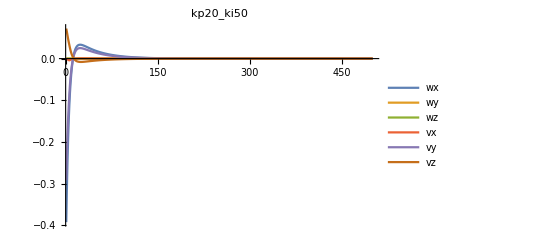

kp20_ki50.gif

kp20_ki50.csv

```mathematica
s[t_]:= 3/25*t^2-2/125*t^3
xdes={{Sin[s[t]*Pi/2],0,Cos[s[t]*Pi/2],s[t]},{0,1,0,0},{-Cos[s[t]*Pi/2],0,Sin[s[t]*Pi/2], 0.491},{0,0,0,1}} ;
vdesbox=Inverse[xdes].D[xdes,t] //FullSimplify;
vdes=se3ToVec[vdesbox] ;
Tsbt={{Cos[ϕ],-Sin[ϕ],0,x},{Sin[ϕ],Cos[ϕ],0,y},{0,0,1,0.0963},{0,0,0,1}};

Blist={{0,0,1,0,0.0330,0},{0,−1,0,−0.5076,0,0},{0,-1,0,−0.3526,0,0},{0,-1,0,−0.2176,0,0},{0,0,1,0,0,0}}ᵀ;
  M={{1,0,0,0.1662+0.0330},{0,1,0,0},{0,0,1,0.0963+0.0026+0.6546},{0,0,0,1}}; 
   eomg=0.01;
  ev=0.001;
timestep=0.01;
dt=0;xdesmat=List[];vdesmat=List[];thetalistmat=List[];dthetalistmat=List[];umat=List[];
velmat=List[];
velmethod2mat=List[];
csv=List[];
xerrmat=List[];
kprop=20;
kint=50;
q00={{-Pi/8,-0.5,0.5}}ᵀ;
(*q00={{0,-0.526,0}}ᵀ;*)
thetalist0={{0,-Pi/4,Pi/4,-Pi/2,0}}ᵀ;

Moe={{1,0,0,0.0330},{0,1,0,0},{0,0,1,0.6546},{0,0,0,1}}; 
 
r=0.0475;l= 0.47/2; w=0.3/2;
f=r/4*{{0,0,0,0},{0,0,0,0},{-1/(l+w),1/(l+w),1/(l+w),-1/(l+w)},{1,1,1,1},{-1,1,-1,1},{0,0,0,0}};

(**)

For[
i=1;
vupdated=List[];
wheelangle=ConstantArray[0,4];
qnew=q00;
cumerr=ConstantArray[0,6],
i≤500,i++,

(*1*)
xdesnow=xdes/.t-> dt //FullSimplify;
xdesmat=AppendTo[xdesmat,xdesnow //Chop] ;
vdesboxi=Inverse[xdes].D[xdes,t] /.t-> dt//FullSimplify;
vdesi=se3ToVec[vdesboxi] //Chop ;
vdesmat=AppendTo[vdesmat,vdesi];

(*2*)

Tsbn=Tsbt /.{ϕ->qnew[[1,1]],x->qnew[[2,1]],y->qnew[[3,1]]};
Tbo={{1,0,0,0.1662},{0,1,0,0},{0,0,1,0.0026},{0,0,0,1}};
Toe = FKinBody[Moe,Blist,thetalist0]//Chop;
xnew=Tsbn.Tbo.Toe;

xerr=se3ToVec[MatrixLog6[Inverse[xnew].xdesnow]];
xerrmat=AppendTo[xerrmat,xerr];
cumerr+=timestep*xerr[[All,1]];

(*3*)
vupdated=(Adjoint[Inverse[xnew].xdesnow].vdesi)[[All,1]]+kprop*xerr[[All,1]]+kint*cumerr//Chop; (*control law*)

(*4*)

Jbase=Adjoint[Inverse[Toe].Inverse[Tbo]].f;
Jarm=JacobianBody[Blist,thetalist0];
Jbmethod2=Join[Jbaseᵀ,Jarmᵀ]ᵀ //Chop;

dthetalist=PseudoInverse[Jbmethod2].vupdated//Chop; (* u and dtheta*)
dthetalistmat=AppendTo[dthetalistmat,dthetalist];

(*5*)
wheelchange=timestep*dthetalist[[;;4]];
wheelangle+=wheelchange;
vbase=r/4*{{-1/(l+w),1/(l+w),1/(l+w),-1/(l+w)},{1,1,1,1},{-1,1,-1,1}}.wheelchange //Chop;

If[
vbase[[1]]==0,
dphi=0;dx=vbase[[2]];dy=vbase[[3]],
dphi=vbase[[1]];dx=(vbase[[2]]*Sin[vbase[[1]]]+vbase[[3]]*(Cos[vbase[[1]]]-1))/vbase[[1]];
dy=(vbase[[3]]*Sin[vbase[[1]]]-vbase[[2]]*(Cos[vbase[[1]]]-1))/vbase[[1]]];

dq={{1,0,0},{0,Cos[qnew[[1,1]]],-Sin[qnew[[1,1]]]},{0,Sin[qnew[[1,1]]],Cos[qnew[[1,1]]]}}.{{dphi},{dx},{dy}};
qnew=qnew+dq;
qcsv={qnew[[2]],qnew[[3]],qnew[[1]]};

thetalist0+=timestep*dthetalist[[5;;]];


csv=AppendTo[csv,Join[qcsvᵀ[[1]],thetalist0ᵀ[[1]],wheelangle]];

dt+=timestep]
name="kp20_ki50"


a=xerrmat[[All,1]]ᵀ[[1]];
b=xerrmat[[All,2]]ᵀ[[1]];
c=xerrmat[[All,3]]ᵀ[[1]];
d=xerrmat[[All,4]]ᵀ[[1]];
e=xerrmat[[All,5]]ᵀ[[1]];
f=xerrmat[[All,6]]ᵀ[[1]];
ListLinePlot[{a,b,c,d,e,f},PlotRange->All,PlotLegends->{"wx","wy","wz","vx","vy","vz"},PlotLabel->name]
Export[name<>".gif",%,ImageResolution-> 500,ImageFormattingWidth-> 1000]
Export[name<>".csv",csv]
```